# Delft’s Silicon device

Connectivity of this device

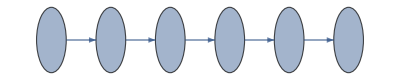

```mathematica
Graph[Range[0,5],Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

Set the default configuration of the device

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->10^5,
(* T2* *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(*rabi frequencies on single rotations; random guess *)
RabiFreq-><|0->8,1->8,2->8,3->7,4->5,5->4|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->True,

(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,

(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9526707113340579,1->0.9395929490898237,2->0.9484194291327452,3->0.9850519102118337,4->0.9663173858117854|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0,1},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2
*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->0.99,
DurRead->10,
RepeatRead->2
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Compilation : QFT

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=SiliconDelft[];
```

```mathematica
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,5];
```

```mathematica
conf["ansatzspace"]={0,1,2};
conf["fixansatz"]={Subscript[Rx, 0][θ],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][θ],Subscript[Ry, 2][θ],Subscript[C, 0][Subscript[Z, 1]],Subscript[C, 1][Subscript[Z, 2]],Subscript[Ry, 2][θ],Subscript[C, 1][Subscript[Z, 2]],Subscript[Ry, 2][θ],Subscript[Rx, 2][θ]};
conf["θinitrange"]=π;
conf["grad"]="SGD";
```

```mathematica
HPsummary@conf
```

{ansatzspace→{0,1,2},dθ→0.01,fixansatz→{Rx_0[θ],C_0[Z_1],Rx_1[θ],Ry_2[θ],C_0[Z_1],C_1[Z_2],Ry_2[θ],C_1[Z_2],Ry_2[θ],Rx_2[θ]},fixansatzparams→<||>,gateset→{Rx_#1[θ]&,Ry_#1[θ]&,C_#1[Z_#2]&},gatespercycle→15,globalconverge→3,grad→SGD,gradstep→0.01,gradstepmultiply→4,greedflat→1/1000,greediness→8,greedinessinit→8,groundstate→0,iterconverge→20,maxbfiter→20,maxgreediter→200,maxpruneiter→300,metignore→1/1000,ngatesinit→30,nqubit→6,parallel→Automatic,perfectingflat→1/100000,pruningerror→0.1,speedupfirst→True,swapfabricdepth→3,usecorr→True,weightgate→{1→0.2,2→0.8},αtikhonov→1/1000,ϵfin→1/1000000,θinitrange→π,ρinit→<|1→0,2→1,3→2,4→3,5→4|>}

```mathematica
CircuitSynthesis[6,conf]
```

Compilation with a fixed ansatz

Set::shape: Lists {ansatz$136943,θvars$136943,idx$136943} and SwapFabric[6,3,π] are not the same shape.

CloneQureg::error: Invalid arguments. See ?CloneQureg

General::stop: Further output of CloneQureg::error will be suppressed during this calculation.

ApplyCircuit::error: Invalid arguments. See ?ApplyCircuit

General::stop: Further output of ApplyCircuit::error will be suppressed during this calculation.

Table::iterb: Iterator {i,RandomGate[<|device→<|DeviceType→SiliconDelft,DeviceDescription→Delft Silicon device with 6-qubits arranged as a linear array with nearest-neighbor connectivity and control qubits are the lower ones.,NumAccessibleQubits→6,«3»,DurationSymbol→VQD`Private`ΔT$9722,Qubits:>{VQD`Private`q$_/;0≤VQD`Private`q$<6:>Association[PassiveNoise→VQD`Private`passivenoisecirc$9722[VQD`Private`q$,VQD`Private`g2$9722,VQD`Private`ΔT$9722]]}|>,parallel→Automatic,«31»,ϵfin→1/(1«5»0),gateset→{{#1}&,{#1}&,{#1,#2}&}|>,«1»]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partd: Part specification KeyAbsent⟦1⟧ is longer than depth of object.

Part::partd: Part specification i⟦1⟧ is longer than depth of object.

Part::partd: Part specification KeyAbsent⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[True,Max[481,1+VQD`Private`p$,1+VQD`Private`q$,1+VQD`Private`p$_,1+VQD`Private`q__,1+VQD`Private`q$_,1+VQD`Private`q$__,1+#1,1+#2]].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[False,!Max[481,1+VQD`Private`p$,1+VQD`Private`q$,1+VQD`Private`p$_,1+VQD`Private`q__,1+VQD`Private`q$_,1+VQD`Private`q$__,1+#1,1+#2]].

Part::partw: Part {2,3} of QuEST`Private`getSymbCtrlsTargs[RandomGate[<|device→<|DeviceType→SiliconDelft,«6»,Qubits:>{VQD`Private`q$_/;0≤VQD`Private`q$<6:>Association[PassiveNoise→VQD`Private`passivenoisecirc$9722[VQD`Private`q$,VQD`Private`g2$9722,VQD`Private`ΔT$9722]]}|>,parallel→Automatic,nqubit→6,«29»,θinitrange→π,ϵfin→1/1000000,gateset→{Rx_#1[θ_(tidx$136943++)]&,Ry_#1[θ_(tidx$136943++)]&,C_#1[Z_#2]&}|>,«1»]] does not exist.

Part::pkspec1: The expression 1«1»QuEST`Private`getSymbCtrlsTargs[RandomGate[<|device→<|DeviceType→SiliconDelft,«6»,Qubits:>{VQD`Private`q$_/;0≤VQD`Private`q$<6:>Association[PassiveNoise→VQD`Private`passivenoisecirc$9722[VQD`Private`q$,VQD`Private`g2$9722,VQD`Private`ΔT$9722]]}|>,parallel→Automatic,nqubit→6,«29»,«12»→π,ϵfin→1/1000000,gateset→{Rx_#1[θ_(tidx$136943++)]&,Ry_#1[θ_(tidx$136943++)]&,C_#1[Z_#2]&}|>,«1»]]«1»«1»⟧ cannot be used as a part specification.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[False,!Max[481,1+VQD`Private`p$,1+VQD`Private`q$,1+VQD`Private`p$_,1+VQD`Private`q__,1+VQD`Private`q$_,1+VQD`Private`q$__,1+#1,1+#2]].

General::stop: Further output of ConstantArray::ilsmn will be suppressed during this calculation.

Part::partw: Part {2,3} of QuEST`Private`getSymbCtrlsTargs[RandomGate[<|device→<|DeviceType→SiliconDelft,«6»,Qubits:>{VQD`Private`q$_/;0≤VQD`Private`q$<6:>Association[PassiveNoise→VQD`Private`passivenoisecirc$9722[VQD`Private`q$,VQD`Private`g2$9722,VQD`Private`ΔT$9722]]}|>,parallel→Automatic,nqubit→6,«29»,θinitrange→π,ϵfin→1/1000000,gateset→{Rx_#1[θ_(tidx$136943++)]&,Ry_#1[θ_(tidx$136943++)]&,C_#1[Z_#2]&}|>,«1»]] does not exist.

Part::pkspec1: The expression 1«1»QuEST`Private`getSymbCtrlsTargs[RandomGate[<|device→<|DeviceType→SiliconDelft,«6»,Qubits:>{VQD`Private`q$_/;0≤VQD`Private`q$<6:>Association[PassiveNoise→VQD`Private`passivenoisecirc$9722[VQD`Private`q$,VQD`Private`g2$9722,VQD`Private`ΔT$9722]]}|>,parallel→Automatic,nqubit→6,«29»,«12»→π,ϵfin→1/1000000,gateset→{Rx_#1[θ_(tidx$136943++)]&,Ry_#1[θ_(tidx$136943++)]&,C_#1[Z_#2]&}|>,«1»]]«1»«1»⟧ cannot be used as a part specification.

Part::partw: Part {2,3} of QuEST`Private`getSymbCtrlsTargs[RandomGate[<|device→<|DeviceType→SiliconDelft,«6»,Qubits:>{VQD`Private`q$_/;0≤VQD`Private`q$<6:>Association[PassiveNoise→VQD`Private`passivenoisecirc$9722[VQD`Private`q$,VQD`Private`g2$9722,VQD`Private`ΔT$9722]]}|>,parallel→Automatic,nqubit→6,«29»,θinitrange→π,ϵfin→1/1000000,gateset→{Rx_#1[θ_(tidx$136943++)]&,Ry_#1[θ_(tidx$136943++)]&,C_#1[Z_#2]&}|>,«1»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression 1«1»QuEST`Private`getSymbCtrlsTargs[RandomGate[<|device→<|DeviceType→SiliconDelft,«6»,Qubits:>{VQD`Private`q$_/;0≤VQD`Private`q$<6:>Association[PassiveNoise→VQD`Private`passivenoisecirc$9722[VQD`Private`q$,VQD`Private`g2$9722,VQD`Private`ΔT$9722]]}|>,parallel→Automatic,nqubit→6,«29»,«12»→π,ϵfin→1/1000000,gateset→{Rx_#1[θ_(tidx$136943++)]&,Ry_#1[θ_(tidx$136943++)]&,C_#1[Z_#2]&}|>,«1»]]«1»«1»⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ConstantArray::argtu: ConstantArray called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of ConstantArray::argtu will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Join[ψθk,{7,8,9,10,11,12}].

CalcExpecPauliSum::error: Invalid arguments. See ?CalcExpecPauliSum

General::stop: Further output of CalcExpecPauliSum::error will be suppressed during this calculation.

$Aborted